# VE401 Recitation 5

## Fisher’s Hypothesis Test

### Hypotheses and Testing

Example: I am a soft drink manufacturer. You are a seller and want to buy my products. I claim that my product has μ≥500ml. You don’t trust me and sampled 20 bottles from my batch.

```mathematica
Data=RandomVariate[NormalDistribution[499,2],20]
```

{499.728,497.006,498.871,500.931,500.157,501.139,495.516,501.89,496.894,497.132,503.624,500.357,498.011,498.447,496.074,502.177,498.081,499.719,497.657,498.895}

```mathematica
Mean[Data]
```

499.115

I claim that the samples are too “extreme” and you are picking bottles with small volumes by chance. Actually, more and more have larger volume. Would you believe me?

Steps:

Figure out the parameter θ and the null value θ_0 you are testing. (θ=μ,θ_0=500 in my example)

Set up a null hypothesis H_0. It can be one of the following: (μ≥500 in my example)

θ=θ_0.

θ≤θ_0.

θ≥θ_0.

Figure out the distribution of the estimator of θ and thus the test statistics. ((X̄-μ)/(σ/√n) follows standard normal distribution. We take Z=(X̄-μ)/(σ/√n) as test statistics)

Analyze data, calculate P-value to see if there is enough evidence of reject H_0.

### Significance or P-value for One-Tailed Test

Intuition: How likely will we observe the data if what I claim is true? How “extreme” is the data? P=P[getting this or even more "extreme" observation|H_0 is true].

```mathematica
IntegralPlot[f_,{x_,L_,U_},{l_,u_},opts:OptionsPattern[]]:=Module[{col=ColorData[1,1]},Plot[{ConditionalExpression[f,x>l&&x<u],f},{x,L,U},Prolog->{{col,Line[{{l,0},{l,f/.{x->l}}}]},{col,Line[{{u,0},{u,f/.{x->u}}}]}},Filling->{1->Axis},PlotStyle->col,opts]]
Manipulate[IntegralPlot[PDF[NormalDistribution[Subscript[μ, 0],2/√20]][x],{x,498,502},{498,Mean[Data]},PlotRange->{0,1.8},Ticks->{{{Subscript[μ, 0],"μ_0"},{Mean[Data],"X̄"},499.5,500.5},Automatic},PlotLabel->"Hypothetical distribution of X̄ with μ_0="<>ToString[Subscript[μ, 0]]],{Subscript[μ, 0],498,502},Paneled->False]
```

In this graph, the distribution is the hypothetical distribution of the estimator according to H_0.

Mathematical representation: Denoting the sample statistics of θ̂ as k, we have

P value=Piecewise[{{P[θ̂≤k|θ=θ_0], if null hypothesis is H_0:θ≥θ_0}, {P[θ̂≥k|θ=θ_0], if null hypothesis is H_0:θ≤θ_0}}]

Example:

##### What is the P-value for my claim that μ≥500ml? Assume that we know true variance σ^2=4 ml^2 and sample statistics X̄=499.115 ml.

For H_0:μ≥500, we calculate (suppose we already know that σ=2).

P[getting more "extreme" observation|H_0 is true]=P[X̄≤ 499.115|μ≥500, σ=2]
   <=P[X̄≤ 499.115|μ=500, σ=2]
=P[(X̄-500)/(2/√20)≤(499.115-500)/(2/√20) ]
=P[Z≤-1.978]
=0.024

```mathematica
CDF[NormalDistribution[],(Mean[Data]-500)/(2/√20)]
```

0.0239544

So, there is at most 2.4% chance to obtain such “extreme” data if my claim is true. Since it is small, so we reject H_0 at the 2.4% level of significance.

### Significance or P-value for Two-Tailed Test

```mathematica
Integral2Plot[f_,{x_,L_,U_},{l_,u_},{l2_,u2_},opts:OptionsPattern[]]:=Module[{col=ColorData[1,1]},Plot[{ConditionalExpression[f,x>l&&x<u||x>l2&&x<u2],f},{x,L,U},Prolog->{{col,Line[{{l2,0},{l2,f/.{x->l2}}}]},
{col,Line[{{u2,0},{u2,f/.{x->u2}}}]},{col,Line[{{l,0},{l,f/.{x->l}}}]},{col,Line[{{u,0},{u,f/.{x->u}}}]}},Filling->{1->Axis},PlotStyle->col,opts]]
Manipulate[Integral2Plot[PDF[NormalDistribution[Subscript[μ, 0],2/√20]][x],{x,498,502},{498,Mean[Data]},{2 Subscript[μ, 0]-Mean[Data],502},PlotRange->{0,1.8},Ticks->{{{Subscript[μ, 0],"μ_0"},{Mean[Data],"X̄"},499.5,500.5},Automatic},PlotLabel->"Hypothetical distribution of X̄ with μ_0="<>ToString[Subscript[μ, 0]]],{Subscript[μ, 0],498,502},Paneled->False]
```

Mathematical representation: Denoting the sample statistics of θ̂ as k, we have

P value=P[|θ̂-θ_0|≥|k-θ_0| |θ=θ_0]  | if null hypothesis is H_0:θ=θ_0

Example:

##### What is the P-value if my claim is μ=500ml? Assume that we know true variance σ^2=4 ml^2 and sample statistics X̄=499.115 ml.

For H_0:μ≥500, we calculate (suppose we already know that σ=2).

P[getting more "extreme" observation|H_0 is true]=P[|X̄-500|≥| 499.115-500||μ=500, σ=2]
   =2P[X̄≤ 499.115|μ=500, σ=1]
=0.048

So, there is at most 4.8% chance to obtain such “extreme” data if my claim is true. Since it is small, so we reject H_0 at the 4.8% level of significance.

## Neyman-Pearson Decision Theory

### Hypotheses and Testing

Steps:

Figure out the parameter θ and the null value θ_0 you are testing.

We set up two competing hypotheses H_0 and H_1. (e.g. H_0:μ≥500, H_1:μ≤499). They can be one of the following: for some δ>0,

H_0:θ=θ_0, H_1:|θ-θ_0|≥δ.

H_0:θ≤θ_0, H_1:θ≥θ_0+δ.

H_0:θ≥θ_0, H_1:θ≤θ_0-δ .

Decide α and β. Calculate the critical region and the sample size.

Analyze data. If the sample statistics lies in the interval of H_1, we accept H_1. Otherwise, we see the whether the sample statistics lies in the critical region. If yes, then reject H_0.

### Type I and Type II Errors

Intuition: Type I error is the case when my claim is falsely rejected. Type II error is the case when my claim is falsely accepted.

|  | In fact | 
 |  | H_0 true | H_0 false
Our choice | Accept H_0 | Good | Type II error
 | Reject H_0 | Type I error | Good

### α and Critical Region

Definition: α=P[Type I error]. The critical region is the interval such that if H_0 is true, the probability of statistics falling into the interval (letting us to reject H_0) is at most α. In other words, the complement of critical region is a 100(1-α)% confidence interval for the parameter.

Usage: If P value≤α, we reject H_0. If sample statistics lies in the critical region, we reject H_0.

Example:

##### We set α=0.05. Calculate the critical region for H_0:μ≥500ml. Assume that we know true variance σ^2=4 ml^2. According to the critical region, should we reject H_0?

We want Z=(X̄-μ_0)/(σ/√n)<-z_0.05 to reject H_0. The critical region is then (-∞,μ_0-z_0.05 σ/(√n))=(-∞,499.264). Since our data X̄=499.115 lies in the critical region, we reject H_0.

```mathematica
Subscript[z, α_]:=InverseCDF[NormalDistribution[],1-α];
500-(2 Subscript[z, 0.05])/(√20)
```

499.264

### β and Sample Size

Definition: β=P[Type II error]=P[Sample statistics lies outside critical region|H_1 true].

Usage:

To calculate a good sample size. n≈((z_(α/2)+z_β)^2 σ^2)/δ^2.

To calculate the power of a test. power=1-β. A powerful test needs smaller sample size, and is more likely to reject H_0.

To plot the OC curve, or β vs. d curve, so that we find n more easily. Here

d=Piecewise[{{(|μ-μ_0|)/σ, if H_0:μ=μ_0}, {(μ-μ_0)/σ, if H_0:μ≤μ_0}, {-(μ-μ_0)/σ, if H_0:μ≥μ_0}}]

Examples:

##### What is the power of my test given that the true mean μ=499ml, true variance σ^2=4 ml^2 and the sample size n=20?

We have d=(|499-500|)/2=0.5,n=20. According to the OC Curve, β≈0.3. So the power is approximately 0.7. So the test is not powerful enough.

##### If the true mean of my product has volume μ=499ml, and the variance is σ^2=4 ml^2, what sample size do we need to get a power of 0.8, if we set α=0.05?

We have d=(|499-500|)/2=0.5. We will need about 30 samples to get a power of 0.8.

```mathematica
((Subscript[z, 0.05]+Subscript[z, 0.2])^2 4)/(499-500)^2
```

24.7302

##### Plot the OC Curve of the test of my product, given α=0.05, sample size n=20 and the variance σ^2=4 ml^2.

In my case H_0:μ≥500, H_1:μ≤499, we need to calculate

P[fail to reject H_0]=P[Sample statistics lies outside critical region]
=P[X̄>499.264|(μ_0-μ)/σ=d]
<=P[X̄>499.264|μ=500-2 d]
=P[(X̄-(500-2d))/(2/√20)>(499.264-(500-2d))/(2/√20)]
=P[Z>(499.264-(500-2d))/(2/√20)]

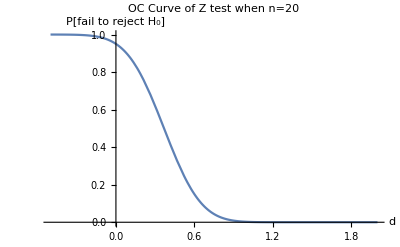

```mathematica
Plot[1-CDF[NormalDistribution[],(499.264-(500-2d))/(2/√20)],{d,-.5,2},AxesLabel->{"d","P[fail to reject H_0]"}, PlotLabel->"OC Curve of Z test when n=20"]
```

When d=0, we can see that β=1-α=0.95.

##### How large should the true mean μ differ from μ_0=500ml so that H_0 is rejected 90% of the time (given H_1 is true)?

According to the OC Curve, at d≈0.65 we obtain β=0.1 or a power of 0.9. This means we need (μ_0-μ)/σ=(500-μ)/2>0.65⇒μ<498.7.

## Null Hypothesis Significance Tests (NHST)

### Hypotheses and Testing

Steps:

Figure out the parameter θ and the null value θ_0 you are testing.

We set up two competing hypotheses H_0 and H_1. (e.g. H_0:μ≥500, H_1:μ≤499). They can be one of the following: for some δ>0,

H_0:θ=θ_0, H_1:θ≠θ_0.

H_0:θ≤θ_0, H_1:θ>θ_0.

H_0:θ≥θ_0, H_1:θ<θ_0.

Decide α.

Analyze data. Calculate the P-value and see if there is enough evidence to reject H_0.

Note: NHST is biased against failing to reject H_0 (too easy to reject H_0).

## Single Sample Tests and Comparison of Parameter

### Test Statistics

From now on, you will learn a lot of tests. For each test, you need to pay attention to:

What parameter are we testing?

What parameter do we know?

What is the distribution of test statistics?

Denoting the distribution of test statistics as 𝒟, and 𝒹_α as the number such that ∫_(-∞)^𝒹_α f_𝒟(x)ⅆx=1-α, we reject at significance level α,

H_0:θ=θ_0 if 𝒟>𝒹_(α/2) or 𝒟<𝒹_(1-α/2). (Test statistics is too small or too big)

H_0:θ≤θ_0 if 𝒟>𝒹_α. (Test statistics is too big)

H_0:θ≥θ_0 if 𝒟<𝒹_(1-α). (Test statistics is too small)

### Single Sample Tests for Mean (Z-Test and T-Test)

Testing 
Parameter | Distribution of X_i | Variance  σ | Sample Size n | Test Statistics | OC Curve x-axis
(for two sided test)
μ | normal | known | any | Z=(X̄-μ_0)/(σ/√n) | d=(|μ-μ_0|)/σ
 | any | known | large |  | 
 | any | unknown | large | Z=(X̄-μ_0)/(S/√n) | d=(|μ-μ_0|)/S
 | normal | unknown | small | T_(n-1)=(X̄-μ_0)/(S/√n) |

Example:

##### If the true variance is unknown, what is the power of my T-test if the true mean is μ=499ml?

```mathematica
(500-499)/(√Variance[Data])
```

0.462933

The corresponding power is about 1-0.35=0.65.

### Single Sample Tests for Variance (Chi-Squared Test)

Testing Parameter | Distribution of X_i | Test Statistics | OC Curve x-axis
(for two sided test)
σ | Normal | χ_(n-1)^2=((n-1)S^2)/σ_0^2 | λ=σ/σ_0

### Single Sample Tests for Median (Non-Parametric)

#### Sign Test for the Median

Testing Parameter | Distribution of X_i | Test Statistics
M | any | Binomial_(n,0.5)=Q_+

where Q_+ is the number of data that lies above M_0. (Usually the data equal to M_0 is discarded).

Example:

```mathematica
Data
```

{499.728,497.006,498.871,500.931,500.157,501.139,495.516,501.89,496.894,497.132,503.624,500.357,498.011,498.447,496.074,502.177,498.081,499.719,497.657,498.895}

##### Test the hypothesis H_0:M≥500ml.

We can count that Q_+=7. P[Q_+≤7]=1/2^20∑_(i=0)^7 (20
i)=0.13. There is no enough evidence to reject H_0.

#### Wilcoxon Signed Rank Test

Testing Parameter | Distribution of X_i | Test Statistics
M | symmetric | W_+

where W_+ is the sum of the positive ranks when ranking |X_i-M_0|. When there is a tie, we take the average value. For example, if the first, second and third smallest |X_i-M_0|  is a group of 3 ties, we rank them all as (1+3)/2=2.
For small n, you can refer to a table of critical values here: http://users.stat.ufl.edu/~winner/tables/wilcox_signrank.pdf. For n≥10, we can approximate the test statistics with E[W]=(n(n+1))/4, Var[W]=(n(n+1)(2n+1))/24. For each group of t ties, the variance is reduced by (t^3-t)/48.

```mathematica
Sort[Data-500]
```

{-4.48438,-3.92626,-3.10595,-2.9944,-2.86761,-2.34263,-1.98916,-1.91898,-1.55252,-1.12854,-1.1048,-0.281418,-0.271902,0.156908,0.356726,0.930833,1.13896,1.89039,2.17724,3.62415}

##### Test the hypothesis H_0:M≥500ml.

We can count that W_+=1+4+5+8+10+13+18=59. According to the table, the critical value for α=0.05 is 60. Since 59<60 we are able to reject H_0 with P<0.05.

```mathematica
Needs["HypothesisTesting`"]
SignedRankTest[Data,500,"TestDataTable",AlternativeHypothesis->"Less"]
```

| Statistic | P-Value
Signed-Rank | 59. | 0.0446939

### Estimation of Proportion

For a Bernoulli random variable X_i, we can calculate p̂=X̄=1/n∑_(i=1)^n x_i. The confidence interval for p would be

p̂±z_(α/2)√(p̂(1-p̂)/n)

If we want to test that |p-p̂|<d for some d>0 with 100(1-α)% confidence, we need the sample size to be at least

n=(z_(α/2)^2 p̂(1-p̂))/d^2≤(z_(α/2)^2)/(4 d^2)

Example:

```mathematica
Data
```

{499.728,497.006,498.871,500.931,500.157,501.139,495.516,501.89,496.894,497.132,503.624,500.357,498.011,498.447,496.074,502.177,498.081,499.719,497.657,498.895}

##### Give a 95% confidence interval of the proportion of good product (with volume ≥500ml) in my batch.

We have p̂=7/20=0.35 and n=20. A confidence interval would be 0.35±0.21.

### Single Sample Test of Proportion (Z-Test)

According to central limit theorem, p̂ is approximately normally distributed with mean p and variance p(1-p)/n.

Testing Parameter | Distribution of X_i | Sample Size | Test Statistics
p | Bernoulli | large | Z=(p̂-p_0)/(√(p_0(1-p_0)/n))

### Comparing Two Proportions (Z-Test, Pooled Test)

Testing Parameter | Distribution of X_i | Sample Size | Hypothesis H_0 | Test Statistics
p_1-p_2 | Bernoulli | large | |p_1-p_2|≥d
for some d≥0 | Z=((p̂)_1-(p̂)_2-(p_1-p_2)_0)/(√(((p̂)_1(1-(p̂)_1))/n_1+((p̂)_2(1-(p̂)_2))/n_2))
 |  |  | p_1=p_2 | Z=((p̂)_1-(p̂)_2)/(√(p̂(1-p̂)(1/n_1+1/n_2)))
where p̂=(n_1(p̂)_1+n_2(p̂)_2)/(n_1+n_2)

### F Distribution

Purpose: To describe the distribution of the ratio of two scaled chi-squared random variables.

Mathematical representation: F_(γ_1,γ_2)=(χ_γ_1^2/γ_1)/(χ_γ_2^2/γ_2)is said to follow an F-distribution with γ_1 and γ_2 degrees of freedom.

Properties:

P[F_(γ_1,γ_2)<x]=1-P[F_(γ_2,γ_1)<1/x].

f_(1-α,γ_1,γ_2)=1/(f_(α,γ_2,γ_1)).

### Comparing Two Variance (F-Test)

Testing Parameter | Distribution of X_i | Test Statistics | Hypothesis H_0 | OC Curve x-axis
(forn_1=n_2=n)
σ_1/σ_2 | Normal | F_(n_1-1,n_2-1)=S_1^2/S_2^2 | σ_1/σ_2≥1
σ_1/σ_2≤1
σ_1/σ_2=1 | λ=σ_1/σ_2

Example:

##### Plot the OC Curve For F-test for sample sizes n_1, n_2.

P[fail to reject H_0]=P[Sample statistics lies outside critical region]
=P[f_(0.975,n_1-1,n_2-1)<S_1^2/S_2^2<f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[(1/σ_1^2)/(1/σ_2^2)f_(0.975,n_1-1,n_2-1)<(S_1^2/σ_1^2)/(S_2^2/σ_2^2)<(1/σ_1^2)/(1/σ_2^2)f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[1/λ^2 f_(0.975,n_1-1,n_2-1)<(S_1^2/σ_1^2)/(S_2^2/σ_2^2)<1/λ^2 f_(0.025,n_1-1,n_2-1)|λ=σ_1/σ_2]
=P[1/λ^2 f_(0.975,n_1-1,n_2-1)<F_(n_1-1,n_2-1)<1/λ^2 f_(0.025,n_1-1,n_2-1)]

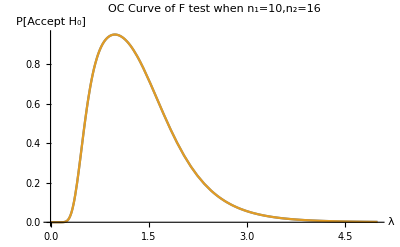

```mathematica
f[λ_,a_,b_]:=CDF[FRatioDistribution[a-1,b-1],1/λ^2 InverseCDF[FRatioDistribution[a-1,b-1],0.975]]-CDF[FRatioDistribution[a-1,b-1],1/λ^2 InverseCDF[FRatioDistribution[a-1,b-1],0.025]];
Plot[{f[λ,10,16],f[1/λ,16,10]},{λ,0,5},PlotLabel->"OC Curve of F test when n_1="<>ToString[10]<>",n_2="<>ToString[16],AxesLabel->{"λ","P[Accept H_0]"}]
```

```mathematica
1/1.1
```

0.909091

```mathematica
1/0.9
```

1.11111

## Problem For Discussion

### Test for Fairness of Coin

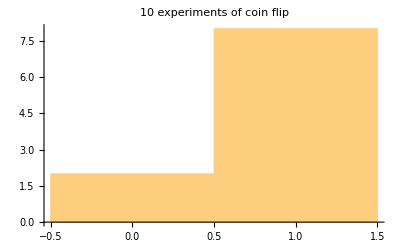

```mathematica
Histogram[RandomInteger[{0,1},10],PlotLabel->"10 experiments of coin flip"]
```

In this discussion, we will explore the essentials for a test. To do this, we ask: How to test the fairness of a coin? The following questions arise.

How to define the “fairness” of a coin? Does p:=P[Heads] have to be 0.5? Is p=0.52 acceptable?

How many experiments will you do for the test?

If you get a certain result (say 8 heads and 2 tails in 10 trials), will you doubt the fairness of the coin?

What is the probability that our conclusion is wrong?

...

We try to give an answer to these questions one by one.

### Definition of “Fairness”

In the real life, p is likely to be normally distributed. In this case P[p=0.5]=0, meaning that almost all coin are not fair. To make it easier to calculate P[fairness], we can define an interval for p, say 0.45<p<0.55, such that if p lies in this interval, we consider the coin to be fair.

### Frequentist Approach

We may calculate the probability of getting the data if p=0.5.

P[getting this or more extreme data]=P[|p̂-0.5|≥0.3|p=0.5]
=2/2^10∑_(i=0)^2 (10
i)
=0.11>0.05

So there is little evidence that the coin is unfair.

### Another Frequentist Approach

We may also think that the sample size is too small to tell us anything. To calculate the appropriate sample size, we take

n=(z_(α/2)^2)/(4 d^2)=1.96^2/(4(0.05)^2)≈385

samples to detect a difference of 0.05 and get a test of significance α=0.05.

```mathematica
Mean[RandomInteger[{0,1},385]]//N
```

0.496104

We then calculate Z=(p̂-p_0)/(√(p_0(1-p_0)/n))=(0.496-0.5)/(√(0.5^2/385))=-0.156. This gives a P-value of 0.876. There is no evidence that the coin is unfair.

### Bayesian Approach

We try to obtain f_P(p):=P[P[Heads]=p]. For simplicity, we use the uniform distribution f_P(p)=1 for 0≤p≤1 (In the reality the distribution may be more concentrated at p=0.5). Using Bayes’ theorem,

f_(P|h Heads and t Tails)(p)=(P[h heads and t tails|P[Heads]=p]f_P(p))/(∫_0^1 P[h heads and t tails|P[Heads]=s]f_P(s)ⅆs)
=((h+t
h)(p^h(1-p))^t)/(∫_0^1 (h+t
h)(s^h(1-s))^t ⅆs)
=((p^h(1-p))^t)/(∫_0^1 (s^h(1-s))^t ⅆs)

This appears to be a beta distribution, and simplifies to

f_(P|h Heads and t Tails)(p)=((h+t+1)!)/(h!t!)(p^h(1-p))^t

Plug in h=8,t=2 gives us the following.

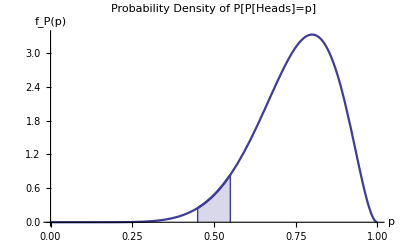

```mathematica
h=8;t=2;
IntegralPlot[((h+t+1)!)/(h!t!)p^h(1-p)^t,{p,0,1},{0.45,0.55},PlotLabel->"Probability Density of P[P[Heads]=p]",AxesLabel->{"p","f_P(p)"}]
```

Then

P[The coin is fair]=∫_0.45^0.55 ((h+t+1)!)/(h!t!)(p^h(1-p))^t ⅆp=0.0504>0.05

The evidence is not strong enough to prove that the coin is unfair.